```mathematica
PacletInstall["https://wolfr.am/DevWQCF",ForceVersionInstall -> True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]

Concept of tensors, and meta information
Meta info is mostly saved as QuantumBasis object
That meta info is basically helping tensors to behave quantum mechanically
Attach basis to a tensor, and one gets a quantum map, generally

```mathematica
QuditName[name,"Dual"->...]
QuditBasis[<|...,{QuditName[...], i} -> tensor,...|>]
QuantumBasis[<|"Input" -> QuditBasis[...],"Output" QuditBasis[...],"Picture"->...,"Label"->...,"ParameterSpec"->...|>]
QuantumState[tensor,  QuantumBasis[...]]
QuantumOperator[QuantumState[...], order]
QuantumMeasurementOperator[QuantumOperator[...], target]
QuantumMeasurement[QuantumMeasurementOperator[...]]
QuantumChannel[QuantumOperator[...]]
QuantumCircuitOperator[<|"Elements" -> ..., "Label" -> ...|>]
```

### QuditName

QuditName is a convenient wrapper around qudit names with unique formatting. It support both bra and ket formatting. Its general input is as follows: QuditName[name,”Dual”->boo], where boo can be True or False.

A qudit name, as Φ, in ket format:

```mathematica
QuditName["Φ","Dual"->True]
```

Φ

A qudit name, as Φ, in bra format:

```mathematica
QuditName["Φ","Dual"->False]
```

Φ

1D qudit: it does not represent a physical qudit, and we will use it as dummy qudit

We should also consider the cases of no qudit, which is defined as follows

```mathematica
QuditName[I, "Dual" -> False]
```

1

We will explain in the following sections why it is important to have a well-defined no-qudit case.

### QuditBasis

The next level of abstraction is QuditBasis, which is a wrapper for an association with keys as names and values as the corresponding tensor representation. 
The key-value has this form: {QuditName[...],qn}->tensor, where qn enumerates qudits.

Print the input form of a 2D qudit basis:

```mathematica
MatrixForm/@QuditBasis[2][[1]]
```

<|{0,1}→(1
0),{1,1}→(0
1)|>

Print the input form of a 2Dx3D qudit basis, in matrix form:

```mathematica
MatrixForm/@QuditBasis[{2,"X"}][[1]]
```

<|{0,1}→(1
0),{1,1}→(0
1),{ψ_(x_-),2}→(-1/(√2)
1/(√2)),{ψ_(x_+),2}→(1/(√2)
1/(√2))|>

Note the actual basis for above example is generated by tensor product of above tensors

```mathematica
MatrixForm/@QuditBasis[{2,"X"}]["Association"]
```

<|0 ψ_(x_-)→(-1/(√2) | 1/(√2)
0 | 0),0 ψ_(x_+)→(1/(√2) | 1/(√2)
0 | 0),1 ψ_(x_-)→(0 | 0
-1/(√2) | 1/(√2)),1 ψ_(x_+)→(0 | 0
1/(√2) | 1/(√2))|>

For example, the first element of above association is generated as

```mathematica
TensorProduct[{1,0},{-1,1}/√2]//MatrixForm
```

(-1/(√2) | 1/(√2)
0 | 0)

As mentioned before, no-qudit basis is defined using no-qudit name

```mathematica
QuditBasis[<|{QuditName[I, "Dual" -> False], 1} -> 1|>]
```

QuditBasis[…]

```mathematica
QuantumBasis[2]//InputForm
```

QuantumBasis[<|"Input" -> QuditBasis[<|{QuditName[I, "Dual" -> False], 1} -> 1|>], 
  "Output" -> QuditBasis[<|{QuditName[0, "Dual" -> False], 1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], 
     {QuditName[1, "Dual" -> False], 1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}]|>], "Picture" -> "Schrödinger", "Label" -> None, 
  "ParameterSpec" -> {}|>]

```mathematica
QuantumBasis[<|"Input" -> QuditBasis[<|{QuditName[I, "Dual" -> False], 1} -> 1|>], 
  "Output" -> QuditBasis[<|{QuditName[0, "Dual" -> False], 1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], 
     {QuditName[1, "Dual" -> False], 1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}]|>], "Picture" -> "Schrödinger", "Label" -> None, 
  "ParameterSpec" -> {}|>]
```

### QuantumBasis

The next level of abstraction is our framework is QuantumBasis. Its generic form is as follows: QuantumBasis[<|“Input” -> QuditBasis[...], “Output” -> QuditBasis[...], “Picture” -> ..., “Label” -> ..., “ParameterSpec” -> ...|>].

Let’s consider a few examples:

As one can see, here the most important additional information are input and output. The rest are what we call as “Meta” data of that quantum object:

```mathematica
QuantumBasis[2]["Meta"]
```

{Picture→Schrödinger,Label→None,ParameterSpec→{}}

Pauli-X quantum basis:

```mathematica
QuantumBasis[2]//InputForm
```

QuantumBasis[<|"Input" -> QuditBasis[<|{QuditName[I, "Dual" -> False], 1} -> 1|>], 
  "Output" -> QuditBasis[<|{QuditName[0, "Dual" -> False], 1} -> SparseArray[Automatic, {2}, 0, 
       {1, {{0, 1}, {{1}}}, {1}}], {QuditName[1, "Dual" -> False], 1} -> SparseArray[Automatic, {2}, 0, 
       {1, {{0, 1}, {{2}}}, {1}}]|>], "Picture" -> "Schrödinger", "Label" -> None, "ParameterSpec" -> {}|>]

Note in this case, there is no input, and only one output

```mathematica
QuantumBasis[2]["Input"]
```

QuditBasis[…]

```mathematica
QuantumBasis[2]["Output"]
```

QuditBasis[…]

The diagram for the basis shows clearly the input and output:

```mathematica
QuantumBasis[2]["Diagram"]
```

-Graphics-

```mathematica
QuantumBasis[{2,3}]["Diagram"]
```

-Graphics-

```mathematica
QuantumBasis[{2},{3}]["InputDimension"]
QuantumBasis[{2},{3}]["OutputDimension"]
```

3

2

Bold -> input -> column indices = covariant
bra

Normal -> output -> row indices = contravariant
ket

```mathematica
QuantumBasis[{2},{2,3}]
```

QuantumBasis[…]

```mathematica
QuantumBasis[2,"X"]
```

QuantumBasis[…]

What is called as basis, in usual QM => same for everything

### QuantumState

The next level of abstraction is QuantumState, which has the general form of QuantumState[tensor,  QuantumBasis[...]], with the tensor can be state vector, density matrix and more.

```mathematica
state=QuantumState[{1,ⅈ,1,ⅈ,3,3ⅈ},{2,3}];
state//InputForm
```

QuantumState[SparseArray[Automatic, {6}, 0, {1, {{0, 6}, {{1}, {2}, {3}, {4}, {5}, {6}}}, 
   {1, I, 1, I, 3, 3*I}}], QuantumBasis[<|"Input" -> QuditBasis[<|{QuditName[I, "Dual" -> False], 1} -> 1|>], 
   "Output" -> QuditBasis[<|{QuditName[0, "Dual" -> False], 1} -> SparseArray[Automatic, {2}, 0, 
        {1, {{0, 1}, {{1}}}, {1}}], {QuditName[1, "Dual" -> False], 1} -> SparseArray[Automatic, {2}, 0, 
        {1, {{0, 1}, {{2}}}, {1}}], {QuditName[0, "Dual" -> False], 2} -> SparseArray[Automatic, {3}, 0, 
        {1, {{0, 1}, {{1}}}, {1}}], {QuditName[1, "Dual" -> False], 2} -> SparseArray[Automatic, {3}, 0, 
        {1, {{0, 1}, {{2}}}, {1}}], {QuditName[2, "Dual" -> False], 2} -> SparseArray[Automatic, {3}, 0, 
        {1, {{0, 1}, {{3}}}, {1}}]|>], "Picture" -> "Schrödinger", "Label" -> None, "ParameterSpec" -> {}|>]]

```mathematica
state["Diagram"]
```

-Graphics-

```mathematica
state["Input"]
```

QuditBasis[…]

```mathematica
state["Output"]
```

QuditBasis[…]

```mathematica
bra=QuantumState["0"]["Dagger"]
```

QuantumState[…]

```mathematica
bra//InputForm
```

QuantumState[SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], 
 QuantumBasis[<|"Input" -> QuditBasis[<|{QuditName[0, "Dual" -> True], 1} -> SparseArray[Automatic, {2}, 0, 
        {1, {{0, 1}, {{1}}}, {1}}], {QuditName[1, "Dual" -> True], 1} -> SparseArray[Automatic, {2}, 0, 
        {1, {{0, 1}, {{2}}}, {1}}]|>], "Output" -> QuditBasis[<|{QuditName[I, "Dual" -> False], 1} -> 1|>], 
   "Picture" -> "Schrödinger", "Label" -> SuperDagger["0"], "ParameterSpec" -> {}|>]]

```mathematica
bra["Diagram"]
```

-Graphics-

```mathematica
bra["Input"]
```

QuditBasis[…]

```mathematica
bra["Output"]
```

QuditBasis[…]

```mathematica
braket=QuantumState["Plus"]["Dagger"]@QuantumState["1"]
```

QuantumState[…]

```mathematica
braket//InputForm
```

QuantumState[SparseArray[Automatic, {1}, 0, {1, {{0, 1}, {{1}}}, {1/Sqrt[2]}}], 
 QuantumBasis[<|"Input" -> QuditBasis[<|{QuditName[I, "Dual" -> False], 1} -> 1|>], "Output" -> QuditBasis[<|{QuditName[I, "Dual" -> False], 1} -> 1|>], 
   "Picture" -> "Schrödinger", "Label" -> SuperDagger["+"] @* "1", "ParameterSpec" -> {}|>]]

```mathematica
ketbra=QuantumState["0"]@QuantumState["1"]["Dagger"]
```

QuantumState[…]

```mathematica
ketbra["Diagram"]
```

-Graphics-

```mathematica
ketbra["Input"]
```

QuditBasis[…]

```mathematica
ketbra["Output"]
```

QuditBasis[…]

```mathematica
ketbra["Basis"]//InputForm
```

QuantumBasis[
 <|"Input" -> QuditBasis[<|{QuditName[0, "Dual" -> True], 1} -> SparseArray[Automatic, {2}, 0, 
       {1, {{0, 1}, {{1}}}, {1}}], {QuditName[1, "Dual" -> True], 1} -> SparseArray[Automatic, {2}, 0, 
       {1, {{0, 1}, {{2}}}, {1}}]|>], 
  "Output" -> QuditBasis[<|{QuditName[0, "Dual" -> False], 1} -> SparseArray[Automatic, {2}, 0, 
       {1, {{0, 1}, {{1}}}, {1}}], {QuditName[1, "Dual" -> False], 1} -> SparseArray[Automatic, {2}, 0, 
       {1, {{0, 1}, {{2}}}, {1}}]|>], "Picture" -> "Schrödinger", "Label" -> "0" @* SuperDagger["1"], 
  "ParameterSpec" -> {}|>]

```mathematica
QuantumOperator["X",{1,4}->{1,3}]["CircuitDiagram"]
```

-Graphics-

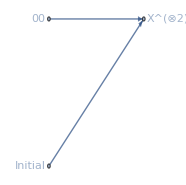

```mathematica
net=QuantumCircuitOperator[{QuantumState["00"],QuantumOperator["X",{1,4}->{1,3}]}]["TensorNetwork",GraphLayout -> {"LayeredDigraphEmbedding", "Orientation" -> Left}]
```

```mathematica
list=Developer`FromPackedArray@VertexList[net];
TableForm[Transpose[Prepend[AnnotationValue[{net,list},#]&/@{"Tensor","Index"},Sort@AnnotationValue[net,VertexLabels]]],]
```

VertexLabel | Tensor | Index
0→Initial | SparseArray[…] | {0^4}
1→00 | SparseArray[…] | {1^1,1^2}
2→X^(⊗2) | SparseArray[…] | {2^1,2^3,2_1,2_4}

```mathematica
EdgeList[net]
```

{12{1^1,2_1},02{0^4,2_4}}

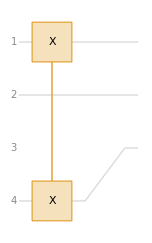

```mathematica
QuantumCircuitOperator[{"X"->{1,4},"Permutation"->{1,4}->{1,3}}]["Diagram"]
```

```mathematica
QuantumCircuitOperator[{"X"->{1,4},"Permutation"->{1,4}->{1,3}}]["CircuitOperator"]==QuantumOperator["X",{1,4}->{1,3}]
```

True

Only output

```mathematica
QuantumOperator[QuantumState["1"]]
```

QuantumOperator[…]

```mathematica
QuantumCircuitOperator[{QuantumOperator[QuantumState["1"]],QuantumOperator@QuantumState[{a,b}]}]
```

QuantumCircuitOperator[…]

```mathematica
QuantumOperator[QuantumState["1"]]["Order"]
```

{{1},{}}

```mathematica
QuantumOperator[QuantumState["1"]]["Tensor"]
```

SparseArray[…]

```mathematica
QuantumOperator[QuantumState[{a,b}]]["Order"]
```

{{1},{}}

```mathematica
?**`Einstein*
```

```mathematica
QuantumState@Flatten@Wolfram`QuantumFramework`PackageScope`EinsteinSummation[{{c[1]},{c[2]}},{QuantumOperator[QuantumState["1"]]["Tensor"],QuantumOperator[QuantumState[{a,b}]]["Tensor"]}]
```

a 10+b 11

```mathematica
QuantumOperator[QuantumState[{a,b,c,d}]]==QuantumOperator[QuantumState[{a,b,c,d}],{1}->{1}]
```

True

```mathematica
QuantumOperator[QuantumState[{a,b,c,d}],{}->{1}]
```

QuantumOperator[…]

```mathematica
QuantumOperator[QuantumState[{a,b,c,d}],{1}->{1}]@QuantumState[{x,y}]
```

QuantumState[…]

### QuantumOperator

The next level of abstraction in our framework is QuantumOperator, which is QuantumOperator[QuantumState[...], order]. In other words, one can see it as a quantum state plus an order, where the order describes where the operator acts.

```mathematica
QuantumOperator["X",{2}]//InputForm
```

QuantumOperator[QuantumState[SparseArray[Automatic, {4}, 0, {1, {{0, 2}, {{2}, {3}}}, {1, 1}}], 
  QuantumBasis[<|"Input" -> QuditBasis[<|{QuditName[0, "Dual" -> True], 1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], 
       {QuditName[1, "Dual" -> True], 1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}]|>], 
    "Output" -> QuditBasis[<|{QuditName[0, "Dual" -> False], 1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], 
       {QuditName[1, "Dual" -> False], 1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}]|>], "Picture" -> "Schrödinger", "Label" -> "X", 
    "ParameterSpec" -> {}|>]], {{2}, {2}}]

```mathematica
QuantumOperator["X",{2}]["Diagram"]
```

-Graphics-

```mathematica
QuantumOperator["X",{2}]["Order"]
```

{{2},{2}}

```mathematica
QuantumOperator["X",{2}]["InputOrder"]
```

{2}

```mathematica
QuantumOperator["X",{2}]["OutputOrder"]
```

{2}

```mathematica
QuantumOperator[QuantumState["1"]["Dagger"],{{},{2}}]//InputForm
```

QuantumOperator[QuantumState[SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}], 
  QuantumBasis[<|"Input" -> QuditBasis[<|{QuditName[0, "Dual" -> True], 1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], 
       {QuditName[1, "Dual" -> True], 1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}]|>], 
    "Output" -> QuditBasis[<|{QuditName[I, "Dual" -> False], 1} -> 1|>], "Picture" -> "Schrödinger", "Label" -> SuperDagger["1"], "ParameterSpec" -> {}|>]], 
 {{}, {2}}]

```mathematica
QuantumOperator[QuantumState["1"]["Dagger"],{{},{2}}]["Diagram"]
```

-Graphics-

```mathematica
op=QuantumOperator[QuantumState["11"]["Dagger"],{1,4}];
op["InputOrder"]
```

{1,4}

```mathematica
op["OutputQudits"]
```

0

```mathematica
op["Diagram"]
```

-Graphics-

```mathematica
QuantumOperator[QuantumState["11"]["Dagger"],{{},{1,4}}]["Diagram"]
```

-Graphics-

```mathematica
QuantumOperator[QuantumState[{a,b,c,d}],{1}->{1}]@QuantumState[{x,y}]
```

(a x+b y) 0+(c x+d y) 1

```mathematica
QuantumOperator[QuantumState[{a,b,c,d}],{}->{1}]@QuantumState[{x,y}]
```

a x 000+a y 001+b x 010+b y 011+c x 100+c y 101+d x 110+d y 111

```mathematica
op=QuantumOperator[QuantumState[{a,b,c,d}]]
```

QuantumOperator[…]

```mathematica
QuantumOperator[QuantumOperator["H"]["State"],{}->{1}][QuantumState[{x,y}]]
```

(x/(√2)+y/(√2)) 0+(x/(√2)-y/(√2)) 1

```mathematica
QuantumOperator[PauliMatrix[1],{}->{1}][QuantumState[{x,y}]]
```

y 0+x 1

### QuantumMeasurementOperator

QuantumMeasurementOperator is abstracted as quantum operator plus target, i.e. QuantumMeasurementOperator[QuantumOperator[...], target]

sum eigen_i proj_i

```mathematica
QuantumMeasurementOperator["X"->{1,-1}]//InputForm
```

QuantumMeasurementOperator[QuantumOperator[QuantumState[SparseArray[Automatic, {4}, 0, {1, {{0, 4}, {{1}, {2}, {3}, {4}}}, {1, 0, 0, -1}}], 
   QuantumBasis[<|"Input" -> QuditBasis[<|{QuditName[Subscript["ψ", Subscript["x", "-"]], "Dual" -> True], 1} -> SparseArray[Automatic, {2}, 0, 
          {1, {{0, 2}, {{1}, {2}}}, {-(1/Sqrt[2]), 1/Sqrt[2]}}], {QuditName[Subscript["ψ", Subscript["x", "+"]], "Dual" -> True], 1} -> 
         SparseArray[Automatic, {2}, 0, {1, {{0, 2}, {{1}, {2}}}, {1/Sqrt[2], 1/Sqrt[2]}}]|>], 
     "Output" -> QuditBasis[<|{QuditName[Subscript["ψ", Subscript["x", "-"]], "Dual" -> False], 1} -> SparseArray[Automatic, {2}, 0, 
          {1, {{0, 2}, {{1}, {2}}}, {-(1/Sqrt[2]), 1/Sqrt[2]}}], {QuditName[Subscript["ψ", Subscript["x", "+"]], "Dual" -> False], 1} -> 
         SparseArray[Automatic, {2}, 0, {1, {{0, 2}, {{1}, {2}}}, {1/Sqrt[2], 1/Sqrt[2]}}]|>], "Picture" -> "Schrödinger", "Label" -> "M", "ParameterSpec" -> {}|>]], 
  {{1}, {1}}], {1}]

```mathematica
Subscript["ψ", Subscript["x", "-"]]Subscript["ψ", Subscript["x", "-"]]-Subscript["ψ", Subscript["x", "+"]]Subscript["ψ", Subscript["x", "+"]]
```

```mathematica
QuantumMeasurementOperator[QuantumOperator[…],{1}]
```

```mathematica
QuantumMeasurementOperator[PauliMatrix[3]]
```

-111+100

```mathematica
-ⅈ (0 1)+ⅈ (1 0)
```

### QuantumMeasurement

```mathematica
QuantumMeasurementOperator[]@QuantumMeasurementOperator[][QuantumState[{1,1}]]
```

QuantumMeasurement[…]

```mathematica
QuantumMeasurementOperator[]["Input"]
```

QuditBasis[…]

```mathematica
%//InputForm
```

QuantumMeasurement[QuantumMeasurementOperator[QuantumOperator[QuantumState[SparseArray[Automatic, {8}, 0, {1, {{0, 2}, {{1}, {8}}}, {1, 1}}], 
    QuantumBasis[<|"Input" -> QuditBasis[<|{QuditName[I, "Dual" -> False], 1} -> 1, {QuditName[I, "Dual" -> False], 2} -> 1|>], 
      "Output" -> QuditBasis[<|{QuditName[Interpretation[Tooltip[Style[0, Bold], "Eigenvalue 1"], {0, {1}}], "Dual" -> False], 1} -> 
          SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], {QuditName[Interpretation[Tooltip[Style[1, Bold], "Eigenvalue 2"], {1, {2}}], "Dual" -> False], 
           1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}], {QuditName[0, "Dual" -> False], 3} -> SparseArray[Automatic, {2}, 0, 
           {1, {{0, 1}, {{1}}}, {1}}], {QuditName[1, "Dual" -> False], 3} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}], 
         {QuditName[Interpretation[Tooltip[Style[0, Bold], "Eigenvalue 1"], {0, {1}}], "Dual" -> False], 2} -> SparseArray[Automatic, {2}, 0, 
           {1, {{0, 1}, {{1}}}, {1}}], {QuditName[Interpretation[Tooltip[Style[1, Bold], "Eigenvalue 2"], {1, {2}}], "Dual" -> False], 2} -> 
          SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}]|>], "Picture" -> "Schrödinger", "Label" -> "M" @* "M" @* None, "ParameterSpec" -> {}|>]], 
   {{-1, 0, 1}, {}}], {1, 1}]]

```mathematica
QuantumMeasurement[QuantumMeasurementOperator[…]]
```

### QuantumChannel

```mathematica
QuantumChannel[{"BitFlip",p},{2,3}]//InputForm
```

QuantumChannel[QuantumOperator[QuantumState[SparseArray[Automatic, {64}, 0, {1, {{0, 16}, {{1}, {6}, {11}, {16}, {18}, {21}, {28}, {31}, {35}, {40}, {41}, {46}, {52}, 
      {55}, {58}, {61}}}, {1 - p, 1 - p, 1 - p, 1 - p, Sqrt[1 - p]*Sqrt[p], Sqrt[1 - p]*Sqrt[p], Sqrt[1 - p]*Sqrt[p], Sqrt[1 - p]*Sqrt[p], Sqrt[1 - p]*Sqrt[p], 
      Sqrt[1 - p]*Sqrt[p], Sqrt[1 - p]*Sqrt[p], Sqrt[1 - p]*Sqrt[p], p, p, p, p}}], 
   QuantumBasis[<|"Output" -> QuditBasis[<|{QuditName[Subscript["K", 0], "Dual" -> False], 1} -> SparseArray[Automatic, {4}, 0, {1, {{0, 1}, {{1}}}, {1}}], 
        {QuditName[Subscript["K", 1], "Dual" -> False], 1} -> SparseArray[Automatic, {4}, 0, {1, {{0, 1}, {{2}}}, {1}}], 
        {QuditName[Subscript["K", 2], "Dual" -> False], 1} -> SparseArray[Automatic, {4}, 0, {1, {{0, 1}, {{3}}}, {1}}], 
        {QuditName[Subscript["K", 3], "Dual" -> False], 1} -> SparseArray[Automatic, {4}, 0, {1, {{0, 1}, {{4}}}, {1}}], 
        {QuditName[0, "Dual" -> False], 2} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], {QuditName[1, "Dual" -> False], 2} -> 
         SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}], {QuditName[0, "Dual" -> False], 3} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], 
        {QuditName[1, "Dual" -> False], 3} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}]|>], 
     "Input" -> QuditBasis[<|{QuditName[0, "Dual" -> True], 2} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], 
        {QuditName[1, "Dual" -> True], 2} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}], {QuditName[0, "Dual" -> True], 3} -> 
         SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], {QuditName[1, "Dual" -> True], 3} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}]|>], 
     "Picture" -> "Schrödinger", "Label" -> "BitFlip"[p], "ParameterSpec" -> {}|>]], {{0, 2, 3}, {2, 3}}]]

```mathematica
QuantumChannel[QuantumOperator[…]]
```

```mathematica
QuantumChannel[{"BitFlip",p},{2}]@QuantumChannel[{"BitFlip",p},{3}]
```

QuantumChannel[QuantumOperator[QuantumState[SparseArray[Automatic, {64}, 0, 
     {1, {{0, 16}, {{1}, {6}, {11}, {16}, {19}, {24}, {25}, {30}, {34}, {37}, {44}, {47}, {52}, {55}, {58}, {61}}}, 
      {1 - p, 1 - p, 1 - p, 1 - p, Sqrt[1 - p]*Sqrt[p], Sqrt[1 - p]*Sqrt[p], Sqrt[1 - p]*Sqrt[p], Sqrt[1 - p]*Sqrt[p], Sqrt[1 - p]*Sqrt[p], Sqrt[1 - p]*Sqrt[p], 
       Sqrt[1 - p]*Sqrt[p], Sqrt[1 - p]*Sqrt[p], p, p, p, p}}], 
    QuantumBasis[Association[Input -> QuditBasis[Association[{QuditName[0, Dual -> False], 1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], 
         {QuditName[1, Dual -> False], 1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}], {QuditName[0, Dual -> False], 2} -> 
          SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], {QuditName[1, Dual -> False], 2} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}]]], 
      Output -> QuditBasis[Association[{QuditName[Subscript[K, 0], Dual -> False], 2} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], 
         {QuditName[Subscript[K, 1], Dual -> False], 2} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}], 
         {QuditName[0, Dual -> False], 3} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], {QuditName[1, Dual -> False], 3} -> 
          SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}], {QuditName[Subscript[K, 0], Dual -> False], 1} -> 
          SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], {QuditName[Subscript[K, 1], Dual -> False], 1} -> 
          SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}], {QuditName[0, Dual -> False], 4} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], 
         {QuditName[1, Dual -> False], 4} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}]]], Picture -> Schrödinger, 
      Label -> BitFlip[p] @* BitFlip[p], ParameterSpec -> {}]]], {{-1, 0, 2, 3}, {2, 3}}]]

```mathematica
QuantumChannel[QuantumOperator[…]]
```

### QuantumCircuitOperator

```mathematica
QuantumCircuitOperator["Bell"]//InputForm
```

QuantumCircuitOperator[
 <|"Elements" -> {QuantumOperator[QuantumState[SparseArray[Automatic, {4}, 0, {1, {{0, 4}, {{1}, {2}, {3}, {4}}}, {1/Sqrt[2], 1/Sqrt[2], 1/Sqrt[2], -(1/Sqrt[2])}}], 
      QuantumBasis[<|"Input" -> QuditBasis[<|{QuditName[0, "Dual" -> True], 1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], 
           {QuditName[1, "Dual" -> True], 1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}]|>], 
        "Output" -> QuditBasis[<|{QuditName[0, "Dual" -> False], 1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], 
           {QuditName[1, "Dual" -> False], 1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}]|>], "Picture" -> "Schrödinger", "Label" -> "H", 
        "ParameterSpec" -> {}|>]], {{1}, {1}}], QuantumOperator[QuantumState[SparseArray[Automatic, {16}, 0, {1, {{0, 4}, {{1}, {6}, {12}, {15}}}, {1, 1, 1, 1}}], 
      QuantumBasis[<|"Input" -> QuditBasis[<|{QuditName[0, "Dual" -> True], 1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], 
           {QuditName[1, "Dual" -> True], 1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}], {QuditName[0, "Dual" -> True], 2} -> 
            SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], {QuditName[1, "Dual" -> True], 2} -> SparseArray[Automatic, {2}, 0, 
             {1, {{0, 1}, {{2}}}, {1}}]|>], "Output" -> QuditBasis[<|{QuditName[0, "Dual" -> False], 1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], 
           {QuditName[1, "Dual" -> False], 1} -> SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {1}}], {QuditName[0, "Dual" -> False], 3} -> 
            SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {1}}], {QuditName[1, "Dual" -> False], 3} -> SparseArray[Automatic, {2}, 0, 
             {1, {{0, 1}, {{2}}}, {1}}]|>], "Picture" -> "Schrödinger", "Label" -> Subscript["C", "NOT"][{1}, {}], "ParameterSpec" -> {}|>]], {{1, 2}, {1, 2}}]}, 
  "Label" -> "Bell"|>]

QuantumCircuitOperator is abstracted as an association with elements as list of operators, ops, and a circuit label, i.e. QuantumCircuitOperator[<|”Elements” -> ops, “Label” -> “Bell”|>]

```mathematica
QuantumCircuitOperator[<|"Elements" -> ops, "Label" -> "Bell"|>]
```

323-783-6908